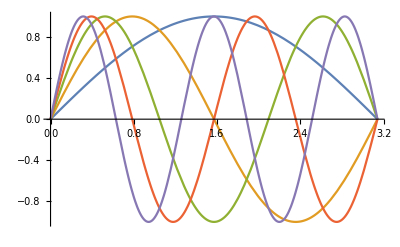

```mathematica
dd=DSolve[{y''[x]+λ y[x]==0,y[0]==0,y[π]==0},y[x],x];
eigfuns=Table[y[x]/.dd[[1]]//.{n->i,λ->n^2}/.{C[1]->1},{i,5}];
Plot[Evaluate[eigfuns],{x,0,Pi}]
```

{{y[x]→Piecewise[{{C[1] Sin[x √λ], n∈ℤ&&n≥1&&λ==(-1/2+n)^2}, {0, True}}]}}

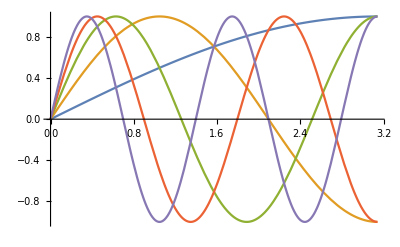

```mathematica
dn=DSolve[{y''[x]+λ y[x]==0,y[0]==0,y'[π]==0},y[x],x]
eigfuns=Table[y[x]/.dn[[1]]//.{n->i,λ->(-1/2+n)^2}/.{C[1]->1},{i,5}];
Plot[Evaluate[eigfuns],{x,0,Pi}]
```

{{y[x]→Piecewise[{{C[1] Cos[x √λ], n∈ℤ&&n≥1&&λ==(-1/2+n)^2}, {0, True}}]}}

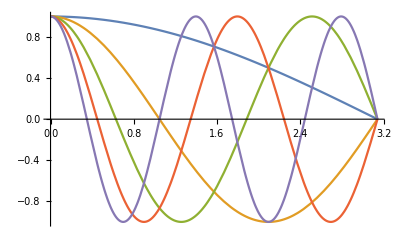

```mathematica
nd=DSolve[{y''[x]+λ y[x]==0,y'[0]==0,y[π]==0},y[x],x]
eigfuns=Table[y[x]/.nd[[1]]//.{n->i,λ->(-1/2+n)^2}/.{C[1]->1},{i,5}];
Plot[Evaluate[eigfuns],{x,0,Pi}]
```

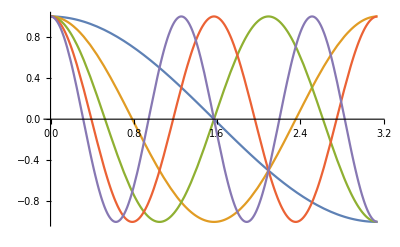

```mathematica
nn=DSolve[{y''[x]+λ y[x]==0,y'[0]==0,y'[π]==0},y[x],x];
eigfuns=Table[y[x]/.nn[[1]]//.{n->i,λ->n^2}/.{C[1]->1},{i,5}];
Plot[Evaluate[eigfuns],{x,0,Pi}]
```